## General Equations for coop and comp

```mathematica
Clear[mu1,mu2,a1,a2,k1,k2,z1,z2,z3,R,v1,v2,δ, v3]
xcoopRHS = mu1*X*((a1*Y)/(a1*Y)+k1)*(R-X)-z1*g*X-δ*X;
ycoopRHS = mu2*Y*((a2*X)/(a2*X)+k2)*(R-Y)-z3*s*Y -z2*g*Y - δ*Y;
xcompRHS = mu1*X*(R-X-b1*Y)-z1*g*X-δ*X;
ycompRHS = mu2*Y*(R-Y-b2*X)-z3*s*Y -z2*g*Y - δ*Y;
gRHS = v2*z2*g*Y + v1*z1*g*X - δ*g;
sRHS = v3*z3*s*Y - δ *s;
fps = Simplify[Solve[{xcoopRHS ==0, ycoopRHS == 0, gRHS == 0, sRHS == 0}, {X,Y,g,s}]];
fpscomp = Simplify[Solve[{xcompRHS ==0, ycompRHS == 0, gRHS == 0, sRHS == 0}, {X,Y,g,s}]];
```

```mathematica
fp10valcoop = FullSimplify[(fps[[10]]//Normal)];
fp10valcomp = FullSimplify[(fpscomp[[10]]//Normal)];
```

```mathematica
Clear[mu1,mu2,a1,a2,k1,k2,z1,z2,z3,R,v1,v2,δ, v3]
xcoopRHS = mu1*X*((a1*Y)/(a1*Y)+k1)*(R-X)-z1*g*X-δ*X;
ycoopRHS = mu2*Y*((a2*X)/(a2*X)+k2)*(R-Y)-z2*s*Y -z1*g*Y - δ*Y;
xcompRHS = mu1*X*(R-X-b1*Y)-z1*g*X-δ*X;
ycompRHS = mu2*Y*(R-Y-b2*X)-z2*s*Y -z1*g*Y - δ*Y;
gRHS = v1*z1*g*Y + v1*z1*g*X - δ*g;
sRHS = v2*z2*s*Y - δ *s;
fps = Simplify[Solve[{xcoopRHS ==0, ycoopRHS == 0, gRHS == 0, sRHS == 0}, {X,Y,g,s}]];
fpscomp = Simplify[Solve[{xcompRHS ==0, ycompRHS == 0, gRHS == 0, sRHS == 0}, {X,Y,g,s}]];
```

```mathematica
fp10valcoop = FullSimplify[(fps[[10]]//Normal)];
fp10valcomp = FullSimplify[(fpscomp[[10]]//Normal)];
fp10valcoop
fp10valcomp
```

{X→δ/(v1 z1)-δ/(v2 z2),Y→δ/(v2 z2),g→(-z1 δ+((1+k1) mu1 (R v1 v2 z1 z2+v1 z1 δ-v2 z2 δ))/(v1 v2 z2))/z1^2,s→((1+k2) mu2 v1 z1 (R v2 z2-δ)-(1+k1) mu1 (R v1 v2 z1 z2+v1 z1 δ-v2 z2 δ))/(v1 v2 z1 z2^2)}

{X→δ/(v1 z1)-δ/(v2 z2),Y→δ/(v2 z2),g→(-z1 δ+mu1 (R z1-δ/v1-((-1+b1) z1 δ)/(v2 z2)))/z1^2,s→((-mu1+mu2) R z2+(((-1+b1) mu1+(-1+b2) mu2) δ)/v2+((mu1-b2 mu2) z2 δ)/(v1 z1))/z2^2}

Coop: fp1 is only S, fp2 is E and S, fp3 is only E, fp4 is E/S/sp, fp5 is S/gen, fp6 is E/S/gen, fp7 is full extinction, fp8 is E/gen, fp9 is S/sp, fp10 is all 4 
Comp: fp1 is E/S, fp2 is S, fp3 is S/gen, fp4 is S/sp, fp5 is E/S/gen, fp6 is is E, fp7 is full extinction, fp8 is E/gen, fp9 is E/S/sp, fp10 is all 4
Focus on: E/S/sp, E/S/gen, all 4 [coop - fp4, fp6, fp10; comp - fp5, fp9, fp10]

## Generalizable coop solutions without fixed parameters

```mathematica
fp1val = FullSimplify[(fps[[1]]//Normal)];
fp2val = FullSimplify[(fps[[2]]//Normal)];
fp3val = FullSimplify[(fps[[3]]//Normal)];
fp4val = FullSimplify[(fps[[4]]//Normal)];
fp5val = FullSimplify[(fps[[5]]//Normal)];
fp6val = FullSimplify[(fps[[6]]//Normal)];
fp7val = FullSimplify[(fps[[7]]//Normal)];
fp8val = FullSimplify[(fps[[8]]//Normal)];
fp9val = FullSimplify[(fps[[9]]//Normal)];
fp10val = FullSimplify[(fps[[10]]//Normal)];
J = {{D[xcoopRHS, X],D[xcoopRHS, Y],D[xcoopRHS, g], D[xcoopRHS, s]},{D[ycoopRHS, X],D[ycoopRHS, Y],D[ycoopRHS, g], D[ycoopRHS, s]},{D[gRHS, X],D[gRHS, Y],D[gRHS, g], D[gRHS, s]},{D[sRHS, X],D[sRHS, Y],D[sRHS, g], D[sRHS, s]} } // FullSimplify;
J10 = J /. fp10val;
det10 = FullSimplify[Det[J10]];
tr10 = FullSimplify[Tr[J10]];
```

## Coop solutions when only specialist gamma is variant

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

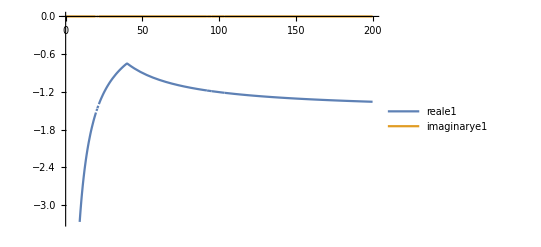

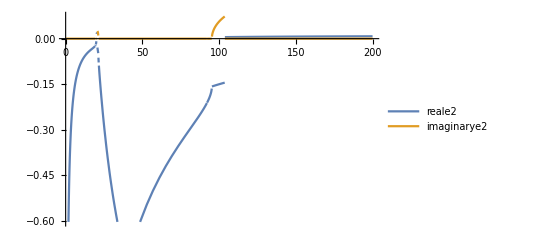

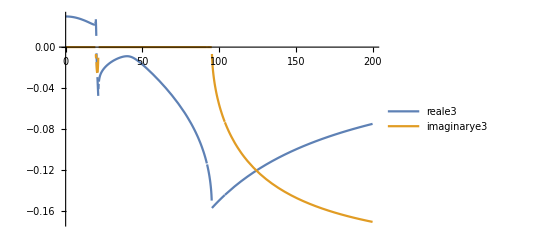

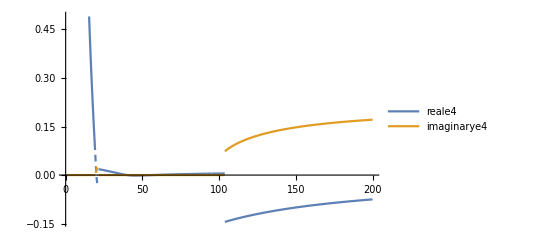

```mathematica
Clear[mu1,mu2,a1,a2,k1,k2,z1,z2,z3,R,v1,v2,δ, v3]
mu1 = 0.5;mu2 = 0.5; a1 = 1; a2 = 1; k1 = 1; k2 = 1; δ = 0.03; z1 = 0.001; z2 = 0.001; z3 = 0.001; v1 = 20; v2 = 20 ; R = 1;
fp1val = FullSimplify[(fps[[1]]//Normal), Assumptions -> {v3 > 0}];
fp2val = FullSimplify[(fps[[2]]//Normal), Assumptions -> {v3 > 0}];
fp3val = FullSimplify[(fps[[3]]//Normal), Assumptions -> {v3 > 0}];
fp4val = FullSimplify[(fps[[4]]//Normal), Assumptions -> {v3 > 0}];
fp5val = FullSimplify[(fps[[5]]//Normal), Assumptions -> {v3 > 0}];
fp6val = FullSimplify[(fps[[6]]//Normal), Assumptions -> {v3 > 0}];
fp7val = FullSimplify[(fps[[7]]//Normal), Assumptions -> {v3 > 0}];
fp8val = FullSimplify[(fps[[8]]//Normal), Assumptions -> {v3 > 0}];
fp9val = FullSimplify[(fps[[9]]//Normal), Assumptions -> {v3 > 0}];
fp10val = FullSimplify[(fps[[10]]//Normal), Assumptions -> {v3 > 0}];
J = {{D[xcoopRHS, X],D[xcoopRHS, Y],D[xcoopRHS, g], D[xcoopRHS, s]},{D[ycoopRHS, X],D[ycoopRHS, Y],D[ycoopRHS, g], D[ycoopRHS, s]},{D[gRHS, X],D[gRHS, Y],D[gRHS, g], D[gRHS, s]},{D[sRHS, X],D[sRHS, Y],D[sRHS, g], D[sRHS, s]} } // FullSimplify;
J10 = J /. fp10val;
det10 = FullSimplify[Det[J10]];
tr10 = FullSimplify[Tr[J10]];
fp10stable = Reduce[{det10 > 0,tr10 < 0, v3 > 0 }, v3];
fp10saddle = Reduce[{det10 < 0, v3 > 0}, v3];
fp10unstable = Reduce[{det10 > 0, tr10 > 0, v3 > 0}, v3];
eigens10 = Solve[Det[J10 - λ*IdentityMatrix[4]]==0, λ];
e1 = -(1.7763568394002505*^-15 (-1.+2.11106232532992*^14 v3))/v3-0.5 √((1.262177448353619*^-29 (-1.+2.11106232532992*^14 v3)^2)/v3^2-(0.0002 (-3.*^6+147000. v3+97. v3^2))/v3^2+(0.009449407874211549 (7.9164837199872*^25 v3^2-7.245165900532285*^24 v3^3+1.2554382095620766*^23 v3^4+2.549477193742811*^21 v3^5-3.044319878502469*^19 v3^6))/(v3^3 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3))+1/v3^3 1.2031107052948752*^-19 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3))-0.5 √((2.524354896707238*^-29 (-1.+2.11106232532992*^14 v3)^2)/v3^2-(0.0004 (-3.*^6+147000. v3+97. v3^2))/v3^2-(0.009449407874211549 (7.9164837199872*^25 v3^2-7.245165900532285*^24 v3^3+1.2554382095620766*^23 v3^4+2.549477193742811*^21 v3^5-3.044319878502469*^19 v3^6))/(v3^3 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3))-1/v3^3 1.2031107052948752*^-19 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3)-(0.25 (-(3.587324068671532*^-43 (-1.+2.11106232532992*^14 v3)^3)/v3^3+(8.526512829121201*^-18 (-1.+2.11106232532992*^14 v3) (-3.*^6+147000. v3+97. v3^2))/v3^3-(0.036 (-240000.+28240. v3-1112. v3^2+15. v3^3))/v3^3))/(√((1.262177448353619*^-29 (-1.+2.11106232532992*^14 v3)^2)/v3^2-(0.0002 (-3.*^6+147000. v3+97. v3^2))/v3^2+(0.009449407874211549 (7.9164837199872*^25 v3^2-7.245165900532285*^24 v3^3+1.2554382095620766*^23 v3^4+2.549477193742811*^21 v3^5-3.044319878502469*^19 v3^6))/(v3^3 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3))+1/v3^3 1.2031107052948752*^-19 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3)))); e2 = -(1.7763568394002505*^-15 (-1.+2.11106232532992*^14 v3))/v3-0.5 √((1.262177448353619*^-29 (-1.+2.11106232532992*^14 v3)^2)/v3^2-(0.0002 (-3.*^6+147000. v3+97. v3^2))/v3^2+(0.009449407874211549 (7.9164837199872*^25 v3^2-7.245165900532285*^24 v3^3+1.2554382095620766*^23 v3^4+2.549477193742811*^21 v3^5-3.044319878502469*^19 v3^6))/(v3^3 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3))+1/v3^3 1.2031107052948752*^-19 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3))+0.5 √((2.524354896707238*^-29 (-1.+2.11106232532992*^14 v3)^2)/v3^2-(0.0004 (-3.*^6+147000. v3+97. v3^2))/v3^2-(0.009449407874211549 (7.9164837199872*^25 v3^2-7.245165900532285*^24 v3^3+1.2554382095620766*^23 v3^4+2.549477193742811*^21 v3^5-3.044319878502469*^19 v3^6))/(v3^3 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3))-1/v3^3 1.2031107052948752*^-19 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3)-(0.25 (-(3.587324068671532*^-43 (-1.+2.11106232532992*^14 v3)^3)/v3^3+(8.526512829121201*^-18 (-1.+2.11106232532992*^14 v3) (-3.*^6+147000. v3+97. v3^2))/v3^3-(0.036 (-240000.+28240. v3-1112. v3^2+15. v3^3))/v3^3))/(√((1.262177448353619*^-29 (-1.+2.11106232532992*^14 v3)^2)/v3^2-(0.0002 (-3.*^6+147000. v3+97. v3^2))/v3^2+(0.009449407874211549 (7.9164837199872*^25 v3^2-7.245165900532285*^24 v3^3+1.2554382095620766*^23 v3^4+2.549477193742811*^21 v3^5-3.044319878502469*^19 v3^6))/(v3^3 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3))+1/v3^3 1.2031107052948752*^-19 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3))));e3 = -(1.7763568394002505*^-15 (-1.+2.11106232532992*^14 v3))/v3+0.5 √((1.262177448353619*^-29 (-1.+2.11106232532992*^14 v3)^2)/v3^2-(0.0002 (-3.*^6+147000. v3+97. v3^2))/v3^2+(0.009449407874211549 (7.9164837199872*^25 v3^2-7.245165900532285*^24 v3^3+1.2554382095620766*^23 v3^4+2.549477193742811*^21 v3^5-3.044319878502469*^19 v3^6))/(v3^3 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3))+1/v3^3 1.2031107052948752*^-19 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3))-0.5 √((2.524354896707238*^-29 (-1.+2.11106232532992*^14 v3)^2)/v3^2-(0.0004 (-3.*^6+147000. v3+97. v3^2))/v3^2-(0.009449407874211549 (7.9164837199872*^25 v3^2-7.245165900532285*^24 v3^3+1.2554382095620766*^23 v3^4+2.549477193742811*^21 v3^5-3.044319878502469*^19 v3^6))/(v3^3 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3))-1/v3^3 1.2031107052948752*^-19 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3)+(0.25 (-(3.587324068671532*^-43 (-1.+2.11106232532992*^14 v3)^3)/v3^3+(8.526512829121201*^-18 (-1.+2.11106232532992*^14 v3) (-3.*^6+147000. v3+97. v3^2))/v3^3-(0.036 (-240000.+28240. v3-1112. v3^2+15. v3^3))/v3^3))/(√((1.262177448353619*^-29 (-1.+2.11106232532992*^14 v3)^2)/v3^2-(0.0002 (-3.*^6+147000. v3+97. v3^2))/v3^2+(0.009449407874211549 (7.9164837199872*^25 v3^2-7.245165900532285*^24 v3^3+1.2554382095620766*^23 v3^4+2.549477193742811*^21 v3^5-3.044319878502469*^19 v3^6))/(v3^3 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3))+1/v3^3 1.2031107052948752*^-19 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3)))); e4 = -(1.7763568394002505*^-15 (-1.+2.11106232532992*^14 v3))/v3+0.5 √((1.262177448353619*^-29 (-1.+2.11106232532992*^14 v3)^2)/v3^2-(0.0002 (-3.*^6+147000. v3+97. v3^2))/v3^2+(0.009449407874211549 (7.9164837199872*^25 v3^2-7.245165900532285*^24 v3^3+1.2554382095620766*^23 v3^4+2.549477193742811*^21 v3^5-3.044319878502469*^19 v3^6))/(v3^3 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3))+1/v3^3 1.2031107052948752*^-19 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3))+0.5 √((2.524354896707238*^-29 (-1.+2.11106232532992*^14 v3)^2)/v3^2-(0.0004 (-3.*^6+147000. v3+97. v3^2))/v3^2-(0.009449407874211549 (7.9164837199872*^25 v3^2-7.245165900532285*^24 v3^3+1.2554382095620766*^23 v3^4+2.549477193742811*^21 v3^5-3.044319878502469*^19 v3^6))/(v3^3 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3))-1/v3^3 1.2031107052948752*^-19 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3)+(0.25 (-(3.587324068671532*^-43 (-1.+2.11106232532992*^14 v3)^3)/v3^3+(8.526512829121201*^-18 (-1.+2.11106232532992*^14 v3) (-3.*^6+147000. v3+97. v3^2))/v3^3-(0.036 (-240000.+28240. v3-1112. v3^2+15. v3^3))/v3^3))/(√((1.262177448353619*^-29 (-1.+2.11106232532992*^14 v3)^2)/v3^2-(0.0002 (-3.*^6+147000. v3+97. v3^2))/v3^2+(0.009449407874211549 (7.9164837199872*^25 v3^2-7.245165900532285*^24 v3^3+1.2554382095620766*^23 v3^4+2.549477193742811*^21 v3^5-3.044319878502469*^19 v3^6))/(v3^3 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3))+1/v3^3 1.2031107052948752*^-19 (-1.5169226451430015*^64 v3^3+2.083083324294248*^63 v3^4-8.233892087383808*^61 v3^5+2.1835996048847474*^57 v3^6+5.036428498323797*^58 v3^7-5.21805911654042*^56 v3^8+5.8042760800825766*^53 v3^9+√(-1.0272161429175562*^127 v3^6+2.800546487521109*^126 v3^7-3.4648274277225955*^125 v3^8+2.726341593690907*^124 v3^9-1.6033534403005235*^123 v3^10+7.233804329635693*^121 v3^11-2.248416230372078*^120 v3^12+3.597510392415736*^118 v3^13+2.0869889902473026*^116 v3^14-2.250109871937281*^115 v3^15+4.49241885329509*^113 v3^16-4.0401339175477114*^111 v3^17+1.4006875694126317*^109 v3^18))^(1/3))));Plot[{Re[e1], Im[e1]}, {v3, 0, 200}, PlotLegends->{"reale1", "imaginarye1"}]
Plot[{ Re[e2], Im[e2]}, {v3, 0, 200}, PlotLegends->{"reale2", "imaginarye2"}]
Plot[{Re[e3], Im[e3]}, {v3, 0, 200}, PlotLegends->{"reale3", "imaginarye3"}]
Plot[{ Re[e4], Im[e4]}, {v3, 0, 200}, PlotLegends->{"reale4", "imaginarye4"}]
```

When v3 is between 3.4 and 20, the FP is stable - the specialist is always lost. The range between 20 and 40 is a saddle point - specialist is still always lost, but pushing toward the threshold at 40 where the specialist is stably maintained. Between 40 and 46, both phage are maintained with abundances > 1 (specialist wins above 42). Between 46 and 56.6038, the generalist is lost and the specialist is maintained with both prey species. Above 56.6038, the threshold is crossed as increases in v3 will lead to extinction of the hosts.

## Coop solutions varying E growth rate and specialist gamma

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

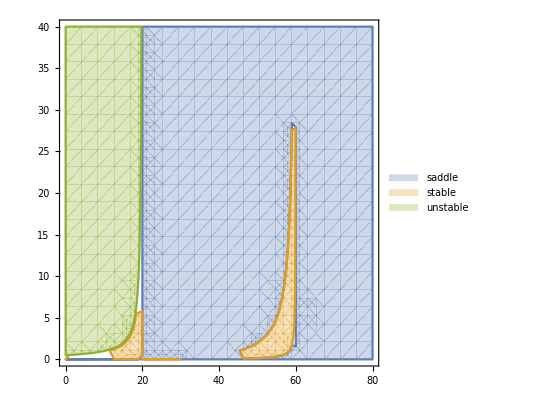

```mathematica
Clear[mu1,mu2,a1,a2,k1,k2,z1,z2,z3,R,v1,v2,δ, v3]
mu2 = 0.5; a1 = 1; a2 = 1; k1 = 1; k2 = 1; δ = 0.03; z1 = 0.001; z2 = 0.001; z3 = 0.001; v1 = 20; v2 = 20 ; R = 1;
fp1val = FullSimplify[(fps[[1]]//Normal), Assumptions -> {v3 > 0, mu1 > 0}];
fp2val = FullSimplify[(fps[[2]]//Normal), Assumptions -> {v3 > 0, mu1 > 0}];
fp3val = FullSimplify[(fps[[3]]//Normal), Assumptions -> {v3 > 0, mu1 > 0}];
fp4val = FullSimplify[(fps[[4]]//Normal), Assumptions -> {v3 > 0, mu1 > 0}];
fp5val = FullSimplify[(fps[[5]]//Normal), Assumptions -> {v3 > 0, mu1 > 0}];
fp6val = FullSimplify[(fps[[6]]//Normal), Assumptions -> {v3 > 0, mu1 > 0}];
fp7val = FullSimplify[(fps[[7]]//Normal), Assumptions -> {v3 > 0, mu1 > 0}];
fp8val = FullSimplify[(fps[[8]]//Normal), Assumptions -> {v3 > 0, mu1 > 0}];
fp9val = FullSimplify[(fps[[9]]//Normal), Assumptions -> {v3 > 0, mu1 > 0}];
fp10val = FullSimplify[(fps[[10]]//Normal), Assumptions -> {v3 > 0, mu1 > 0}];
J = {{D[xcoopRHS, X],D[xcoopRHS, Y],D[xcoopRHS, g], D[xcoopRHS, s]},{D[ycoopRHS, X],D[ycoopRHS, Y],D[ycoopRHS, g], D[ycoopRHS, s]},{D[gRHS, X],D[gRHS, Y],D[gRHS, g], D[gRHS, s]},{D[sRHS, X],D[sRHS, Y],D[sRHS, g], D[sRHS, s]} } // FullSimplify;
J10 = J /. fp10val;
det10 = FullSimplify[Det[J10]];
tr10 = FullSimplify[Tr[J10]];
fp10stable = Reduce[{det10 > 0,tr10 < 0,tr10^2-4 det10 > 0, v3 > 0, mu1 > 0 }, {v3, mu1}];
fp10saddle = Reduce[{det10 < 0, v3 > 0, mu1 > 0}, {v3, mu1}];
fp10unstable = Reduce[{det10 > 0, tr10 > 0, v3 > 0, mu1 > 0}, {v3, mu1}];
RegionPlot[{Evaluate@fp10saddle,Evaluate@fp10stable, Evaluate@fp10unstable} , {v3, 0, 80}, {mu1, 0, 40}, PlotLegends->{"saddle", "stable", "unstable"}]
```

## Coop solutions varying specialist consumption

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

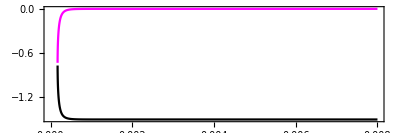

```mathematica
Clear[mu1,mu2,a1,a2,k1,k2,z1,z2,z3,R,v1,v2,δ, v3]
mu1 = 0.5;mu2 = 0.5; a1 = 1; a2 = 1; k1 = 1; k2 = 1; δ = 0.03; z1 = 0.001; z2 = 0.001; v1 = 20; v2 = 20 ; R = 1; v3 = 20;
fp1val = FullSimplify[(fps[[1]]//Normal), Assumptions -> {z3 > 0}];
fp2val = FullSimplify[(fps[[2]]//Normal), Assumptions -> {z3 > 0}];
fp3val = FullSimplify[(fps[[3]]//Normal), Assumptions -> {z3 > 0}];
fp4val = FullSimplify[(fps[[4]]//Normal), Assumptions -> {z3 > 0}];
fp5val = FullSimplify[(fps[[5]]//Normal), Assumptions -> {z3 > 0}];
fp6val = FullSimplify[(fps[[6]]//Normal), Assumptions -> {z3 > 0}];
fp7val = FullSimplify[(fps[[7]]//Normal), Assumptions -> {z3 > 0}];
fp8val = FullSimplify[(fps[[8]]//Normal), Assumptions -> {z3 > 0}];
fp9val = FullSimplify[(fps[[9]]//Normal), Assumptions -> {z3 > 0}];
fp10val = FullSimplify[(fps[[10]]//Normal), Assumptions -> {z3 > 0}];
J = {{D[xcoopRHS, X],D[xcoopRHS, Y],D[xcoopRHS, g], D[xcoopRHS, s]},{D[ycoopRHS, X],D[ycoopRHS, Y],D[ycoopRHS, g], D[ycoopRHS, s]},{D[gRHS, X],D[gRHS, Y],D[gRHS, g], D[gRHS, s]},{D[sRHS, X],D[sRHS, Y],D[sRHS, g], D[sRHS, s]} } // FullSimplify;
J10 = J /. fp10val;
det10 = FullSimplify[Det[J10]];
tr10 = FullSimplify[Tr[J10]];
fp10stable = Reduce[{det10 > 0,tr10 < 0,tr10^2-4 det10 > 0, z3 > 0 }, z3];
fp10saddle = Reduce[{det10 < 0, z3 > 0}, z3];
fp10unstable = Reduce[{det10 > 0, tr10 > 0, z3 > 0}, z3];
λ6a=1/2(tr10+√(tr10^2-4det10)); λ6b=1/2(tr10-√(tr10^2-4det10));
Plot[{λ6a,λ6b},{z3,0,0.008},Axes->True,Frame->True,AxesOrigin->{0,0},PlotStyle->{Directive[Magenta],Directive[Black]},AspectRatio->1/3]
```

```mathematica
Solve[Det[J10 - λ*IdentityMatrix[4]]==0, λ]
```

When z3 is between 0.00017 and 0.001, the FP is stable - the specialist is always lost. The range between 0.001 and 0.002 is a saddle point - specialist is still always lost, but pushing toward the threshold at 0.002 where the specialist is stably maintained. Between 0.002 and 0.0023, both phage are maintained with abundances > 1 (specialist wins above 0.002). Between 0.0023 and 0.00283019, the generalist is lost and the specialist is maintained with both prey species. Above 0.00283109, the threshold is crossed as increases in z3 will lead to extinction of the hosts.

## Coop solutions varying E alpha and specialist gamma

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

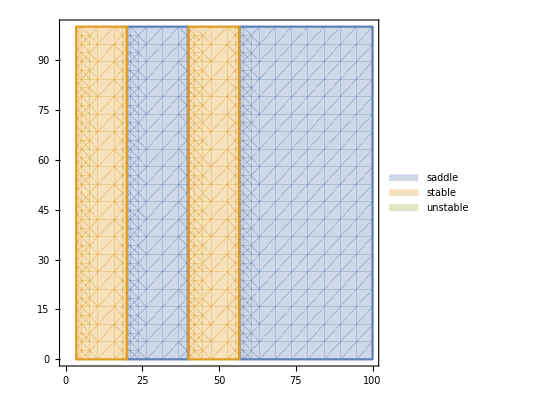

```mathematica
Clear[mu1,mu2,a1,a2,k1,k2,z1,z2,z3,R,v1,v2,δ, v3]
mu1 = 0.5; mu2 = 0.5; a2 = 1; k1 = 1; k2 = 1; δ = 0.03; z1 = 0.001; z2 = 0.001; z3 = 0.001; v1 = 20; v2 = 20 ; R = 1;
fp1val = FullSimplify[(fps[[1]]//Normal), Assumptions -> {v3 > 0, a1 > 0}];
fp2val = FullSimplify[(fps[[2]]//Normal), Assumptions -> {v3 > 0, a1 > 0}];
fp3val = FullSimplify[(fps[[3]]//Normal), Assumptions -> {v3 > 0, a1 > 0}];
fp4val = FullSimplify[(fps[[4]]//Normal), Assumptions -> {v3 > 0, a1 > 0}];
fp5val = FullSimplify[(fps[[5]]//Normal), Assumptions -> {v3 > 0, a1 > 0}];
fp6val = FullSimplify[(fps[[6]]//Normal), Assumptions -> {v3 > 0, a1 > 0}];
fp7val = FullSimplify[(fps[[7]]//Normal), Assumptions -> {v3 > 0, a1 > 0}];
fp8val = FullSimplify[(fps[[8]]//Normal), Assumptions -> {v3 > 0, a1 > 0}];
fp9val = FullSimplify[(fps[[9]]//Normal), Assumptions -> {v3 > 0, a1 > 0}];
fp10val = FullSimplify[(fps[[10]]//Normal), Assumptions -> {v3 > 0, a1 > 0}];
J = {{D[xcoopRHS, X],D[xcoopRHS, Y],D[xcoopRHS, g], D[xcoopRHS, s]},{D[ycoopRHS, X],D[ycoopRHS, Y],D[ycoopRHS, g], D[ycoopRHS, s]},{D[gRHS, X],D[gRHS, Y],D[gRHS, g], D[gRHS, s]},{D[sRHS, X],D[sRHS, Y],D[sRHS, g], D[sRHS, s]} } // FullSimplify;
J10 = J /. fp10val;
det10 = FullSimplify[Det[J10]];
tr10 = FullSimplify[Tr[J10]];
fp10stable = Reduce[{det10 > 0,tr10 < 0,tr10^2-4 det10 > 0,v3 > 0, a1 > 0}, {a1, v3}];
fp10saddle = Reduce[{det10 < 0, v3 > 0, a1 > 0}, {a1, v3}];
fp10unstable = Reduce[{det10 > 0, tr10 > 0, v3 > 0, a1 > 0}, {a1, v3}];
RegionPlot[{Evaluate@fp10saddle,Evaluate@fp10stable, Evaluate@fp10unstable} , {v3, 0, 100}, {a1, 0, 100}, PlotLegends->{"saddle", "stable", "unstable"}]
```

Changing alpha doesn’t push our equations in any particular direction.

## Coop solution varying E growth rate and specialist consumption

```mathematica
Clear[mu1,mu2,a1,a2,k1,k2,z1,z2,z3,R,v1,v2,v3, δ]
mu2 = 0.5; a1 = 1; a2 = 1; k1 = 1; k2 = 1; δ = 0.03; z1 = 0.001; z2 = 0.001;  v1 = 20; v2 = 20 ; v3 = 20; R = 1;
fp1val = FullSimplify[(fps[[1]]//Normal), Assumptions -> {z3 > 0, mu1 > 0}];
fp2val = FullSimplify[(fps[[2]]//Normal), Assumptions -> {z3 > 0, mu1 > 0}];
fp3val = FullSimplify[(fps[[3]]//Normal), Assumptions -> {z3 > 0, mu1 > 0}];
fp4val = FullSimplify[(fps[[4]]//Normal), Assumptions -> {z3 > 0, mu1 > 0}];
fp5val = FullSimplify[(fps[[5]]//Normal), Assumptions -> {z3 > 0, mu1 > 0}];
fp6val = FullSimplify[(fps[[6]]//Normal), Assumptions -> {z3 > 0, mu1 > 0}];
fp7val = FullSimplify[(fps[[7]]//Normal), Assumptions -> {z3 > 0, mu1 > 0}];
fp8val = FullSimplify[(fps[[8]]//Normal), Assumptions -> {z3 > 0, mu1 > 0}];
fp9val = FullSimplify[(fps[[9]]//Normal), Assumptions -> {z3 > 0, mu1 > 0}];
fp10val = FullSimplify[(fps[[10]]//Normal), Assumptions -> {z3 > 0, mu1 > 0}];
J = {{D[xcoopRHS, X],D[xcoopRHS, Y],D[xcoopRHS, g], D[xcoopRHS, s]},{D[ycoopRHS, X],D[ycoopRHS, Y],D[ycoopRHS, g], D[ycoopRHS, s]},{D[gRHS, X],D[gRHS, Y],D[gRHS, g], D[gRHS, s]},{D[sRHS, X],D[sRHS, Y],D[sRHS, g], D[sRHS, s]} } // FullSimplify;
J10 = J /. fp10val;
det10 = FullSimplify[Det[J10]];
tr10 = FullSimplify[Tr[J10]];
fp10stable = Reduce[{det10 > 0,tr10 < 0,tr10^2-4 det10 > 0, z3 > 0, mu1 > 0 }, {z3, mu1}];
fp10saddle = Reduce[{det10 < 0, z3 > 0, mu1 > 0}, {z3, mu1}];
fp10unstable = Reduce[{det10 > 0, tr10 > 0, z3 > 0, mu1 > 0}, {z3, mu1}];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

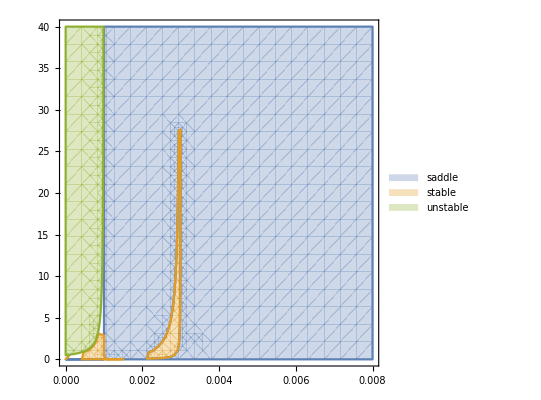

```mathematica
RegionPlot[{Evaluate@fp10saddle,Evaluate@fp10stable, Evaluate@fp10unstable} , {z3, 0, 0.008}, {mu1, 0, 40}, PlotLegends->{"saddle", "stable", "unstable"}]
```

## Coop solutions for generalist preference

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

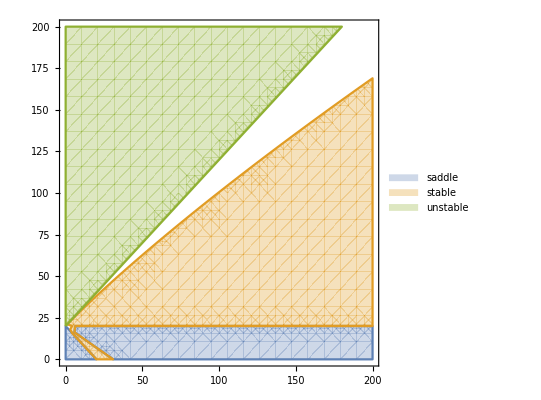

```mathematica
Clear[mu1,mu2,a1,a2,k1,k2,z1,z2,z3,R,v1,v2,v3, δ]
mu1 = 0.5; mu2 = 0.5; a1 = 1; a2 = 1; k1 = 1; k2 = 1; δ = 0.03; z1 = 0.001; z2 = 0.001;v3 = 20; R = 1; z3 = 0.001;
fp1val = FullSimplify[(fps[[1]]//Normal), Assumptions -> {v1 > 0, v2 > 0}];
fp2val = FullSimplify[(fps[[2]]//Normal), Assumptions -> {v1 > 0, v2 > 0}];
fp3val = FullSimplify[(fps[[3]]//Normal), Assumptions -> {v1 > 0, v2 > 0}];
fp4val = FullSimplify[(fps[[4]]//Normal), Assumptions -> {v1 > 0, v2 > 0}];
fp5val = FullSimplify[(fps[[5]]//Normal), Assumptions -> {v1 > 0, v2 > 0}];
fp6val = FullSimplify[(fps[[6]]//Normal), Assumptions -> {v1 > 0, v2 > 0}];
fp7val = FullSimplify[(fps[[7]]//Normal), Assumptions -> {v1 > 0, v2 > 0}];
fp8val = FullSimplify[(fps[[8]]//Normal), Assumptions -> {v1 > 0, v2 > 0}];
fp9val = FullSimplify[(fps[[9]]//Normal), Assumptions -> {v1 > 0, v2 > 0}];
fp10val = FullSimplify[(fps[[10]]//Normal), Assumptions -> {v1 > 0, v2 > 0}];
J = {{D[xcoopRHS, X],D[xcoopRHS, Y],D[xcoopRHS, g], D[xcoopRHS, s]},{D[ycoopRHS, X],D[ycoopRHS, Y],D[ycoopRHS, g], D[ycoopRHS, s]},{D[gRHS, X],D[gRHS, Y],D[gRHS, g], D[gRHS, s]},{D[sRHS, X],D[sRHS, Y],D[sRHS, g], D[sRHS, s]} } // FullSimplify;
J10 = J /. fp10val;
det10 = FullSimplify[Det[J10]];
tr10 = FullSimplify[Tr[J10]];
fp10stable = Reduce[{det10 > 0,tr10 < 0,tr10^2-4 det10 > 0, v1 > 0, v2 > 0 }, {v1, v2}];
fp10saddle = Reduce[{det10 < 0, v1 > 0, v2 > 0},{v1, v2}];
fp10unstable = Reduce[{det10 > 0, tr10 > 0,v1 > 0, v2 > 0}, {v1, v2}];
RegionPlot[{Evaluate@fp10saddle,Evaluate@fp10stable, Evaluate@fp10unstable} , {v1, 0, 200}, {v2, 0, 200}, PlotLegends->{"saddle", "stable", "unstable"}]
```

## Coop solutions for generalist preference with specialist advantage